-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 3 I.G Approach to Equilibrium and Thermodynamic Potentials

```mathematica
(*-------------------------------------*)
t1=TimeObject[{7,0,0}];
t2=TimeObject[{7,10,0}];
Lab1="Thermo.&Stat.\nGeneral Picture";
(*-------------------------------------*)
(*-------------------------------------*)
t3=TimeObject[{7,8,0}];
t4=TimeObject[{7,30,0}];
Lab2="Thermo.&Stat.\nMindMap Lecture";
(*-------------------------------------*)
(*-------------------------------------*)
t5=TimeObject[{8,2,0}];
t6=TimeObject[{8,20,0}];
Lab3="Thermo.&Stat.\nStudents talks";
(*-------------------------------------*)
(*-------------------------------------*)
t71=TimeObject[{8,5,0}];
t81=TimeObject[{8,10,0}];
Lab41="Thermo.&Stat.\nBreak";
(*-------------------------------------*)
(*-------------------------------------*)
t7=TimeObject[{7,35,0}];
t8=TimeObject[{8,45,0}];
Lab4="Thermo.&Stat.\nSlides";
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
t72=TimeObject[{8,50,0}];
t82=TimeObject[{9,0,0}];
Lab42=Hyperlink[Style["Thermo.&Stat.\n   Questions?\n   &\n   Chat..."],"https://mmaitex-gemmini.fly.dev/"];

TS1=TimelinePlot[{
Interval[{t1,t2}]->Lab1,
Interval[{t3,t4}]->Lab2,
Interval[{t5,t6}]->Lab3,
Interval[{t71,t81}]->Lab41,
Interval[{t7,t8}]->Lab4,
Interval[{t72,t82}]->Lab42
},
Frame->True,
FrameStyle->Directive[Thickness[0.003],FontFamily->"Comic Sans MS", FontSize->28],
LabelStyle->Directive[FontFamily->"Comic Sans MS",Black,18],ImageSize->800,Background->LightBlue,AspectRatio->0.35
]
```

-Graphics-

## Functions (run cells)

```mathematica
<<MaTeX`
(* ====================================================*)
(* == Para Integrales bonitas == *)
IntegralOperator/:MakeBoxes[IntegralOperator[x__],form_]:=With[{sub=RowBox@BoxForm`MakeInfixForm[{x},",",form]},InterpretationBox[SubscriptBox["∫",sub],IntegralOperator[x]]]
(* ====================================================*)
(* ====================================================*)
(* === Para escribir derivadas muy bonitas ==*)
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
(* == Para derivadas Parciales bonitas == *)
DifferentialOperator/:MakeBoxes[DifferentialOperator[x__],form_]:=With[{sub=RowBox@BoxForm`MakeInfixForm[{x},",",form]},InterpretationBox[SubscriptBox["∂",sub],DifferentialOperator[x]]]
(* ====================================================*)
(* == Para derivadas Totales bonitas == *)
TotalDifferentialOperator/:MakeBoxes[TotalDifferentialOperator[x__],form_]:=With[{sub=RowBox@BoxForm`MakeInfixForm[{x},",",form]},InterpretationBox[SubscriptBox["d",""],TotalDifferentialOperator[x]]]
```

## What we need to know:

### Gaussian distribution 1D:

(ⅇ^(-x^2/2))/(√(2 π))

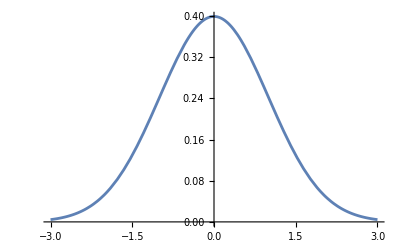

```mathematica
myPDF=PDF[NormalDistribution[0,1],x]
Plot[myPDF,{x,-3,3}]
```

```mathematica
myProba=Integrate[myPDF,{x,0.5,1.0}]
```

0.149882

#### The mean for a gaussian:

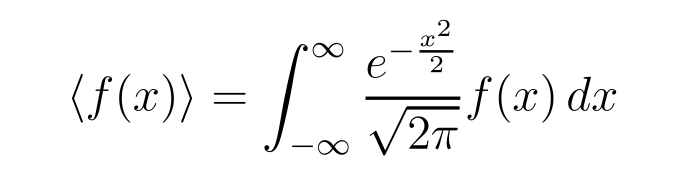

```mathematica
myFave=⟨f[x]⟩==Integrate[TraditionalForm[(myPDF)]*f[x],{x,-∞,+∞}];
Framed[MaTeX[myFave,Magnification->5]]
```

#### In General 1D:

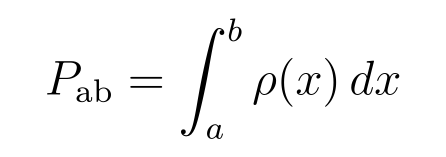

#### In General 1D:

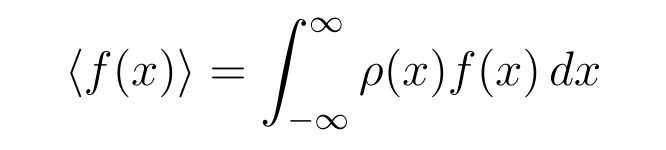

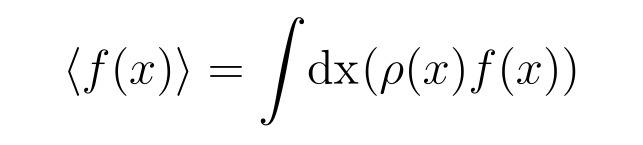

```mathematica
myFave=⟨f[x]⟩==Integrate[HoldForm[ρ[x]*f[x]],{x,-∞,+∞}];
Framed[MaTeX[myFave,Magnification->5]]
myFave=⟨f[x]⟩==IntegralOperator[x][HoldForm[ρ[x]*f[x]]];
Framed[MaTeX[myFave,Magnification->5]]
```

### Dot products

```mathematica
J={Jx,Jy,Jz}
x={V, T, μ}
r=Framed["J⃗·x⃗"]==J.x;
MaTeX[r,Magnification->5]
```

{Jx,Jy,Jz}

{V,T,μ}

-Graphics-

```mathematica
Clear[J,x,y]
r=Framed["d(J⃗·x⃗ )"]==D[(J[y].x[y]),y];
MaTeX[r,Magnification->3]
```

-Graphics-

### Differentials

```mathematica
Clear[f,f1,r,x];
Nvars=2;
arg=Sequence[Subscript[x, 1],Subscript[x, 2]];
f1=∑_(i=1)^Nvars TraditionalForm[pdConv[D[f[arg],Subscript[x, i]]]*TotalDifferentialOperator[x][Subscript[x, i]]];
r=TotalDifferentialOperator[x][f[arg]]==f1;
MaTeX[r,Magnification->3]
```

-Graphics-

### Derivatives

```mathematica
Clear[f,x];
f=1/x;
r=DifferentialOperator[x][f]==pdConv[D[f,x]];
MaTeX[r,Magnification->3]
```

-Graphics-

```mathematica
Clear[f,x];
f=Log[x];
r=DifferentialOperator[x][f]==pdConv[D[f,x]];
MaTeX[r,Magnification->3]
```

-Graphics-

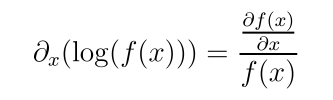

```mathematica
Clear[f,x];
f1=Log[f[x]];
r=DifferentialOperator[x][f1]==pdConv[D[f1,x]];
MaTeX[r,Magnification->3]
```

### Integrals:

```mathematica
Clear[f,x];
f1=1/x;
r=IntegralOperator[x][f1]==Integrate[f1,x];
MaTeX[r,Magnification->3]
```

-Graphics-

### Exponentials

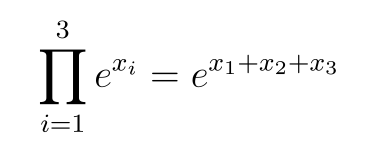

```mathematica
Clear[f,x];
Nvars=3;
f1=∏_(i=1)^Nvars Power[ⅇ,Subscript[x, i]];
r=HoldForm[∏_(i=1)^3 Power[ⅇ,Subscript[x, i]]]==f1;
MaTeX[r,Magnification->4]
```

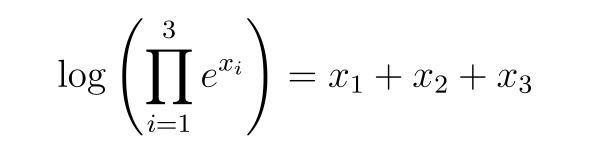

```mathematica
Clear[f,x];
Nvars=3;
f=∏_(i=1)^Nvars Power[ⅇ,Subscript[x, i]];
r=Log[HoldForm[∏_(i=1)^3 Power[ⅇ,Subscript[x, i]]]]==PowerExpand[Log[f]];
MaTeX[r,Magnification->4]
```

### Logarithms

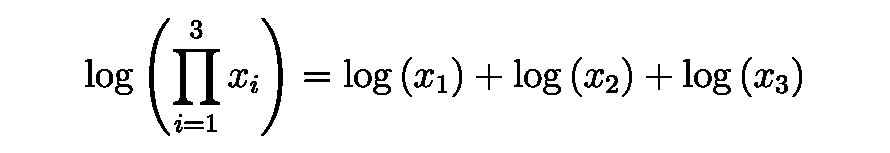

```mathematica
Clear[f];
Nvars=3;
f=∑_(i=1)^Nvars Log[Subscript[x, i]];
r=Log[HoldForm[∏_(i=1)^3 Subscript[x, i]]]==f;
MaTeX[r,Magnification->4]
```

Thermodynamics of Non-Equilibrium Systems

The second law of thermodynamics governs the evolution of non-equilibrium systems toward equilibrium. In the previous section, we demonstrated that for an adiabatically isolated system, the entropy must increase during any spontaneous change and reaches a maximum at equilibrium. However, what about out-of-equilibrium systems that are not adiabatically isolated and may be subjected to external mechanical work?

In such cases, it is often possible to define other thermodynamic potentials that are extremized when the system attains equilibrium. These potentials, derived from appropriate combinations of thermodynamic variables, provide a framework for analyzing the behavior of non-equilibrium systems under various constraints and external influences.

The choice of the appropriate thermodynamic potential depends on the specific conditions imposed on the system. For instance, the Helmholtz free energy is minimized at equilibrium for systems held at constant temperature and volume, while the Gibbs free energy is minimized for systems maintained at constant temperature and pressure. These potentials encapsulate the interplay between energy, entropy, and the external constraints, enabling the prediction of equilibrium states and the determination of spontaneous processes.

By employing the relevant thermodynamic potential, one can quantify the driving forces for processes occurring in non-equilibrium systems and establish criteria for equilibrium conditions. Furthermore, the extremization principles associated with these potentials provide a powerful tool for analyzing phase transitions, chemical reactions, and other phenomena involving the exchange of energy, matter, and entropy between the system and its surroundings.

(2) -- Enthalpy emerges as the appropriate thermodynamic potential when the system undergoes no heat exchange (dQ=0) and attains mechanical equilibrium with a constant external force. The minimum enthalpy principle encapsulates the observation that stable mechanical equilibrium corresponds to the minimization of the net potential energy of the system coupled with the external agent.

Consider an illustrative example: a spring with natural length L0 and spring constant K, subjected to the force exerted by a particle of mass m. For an extension x=L-L0, the internal energy of the spring is Kx^2/2, while the potential energy of the particle changes by -mgx. Mechanical equilibrium is realized by minimizing Kx^2/2-mgx, yielding an equilibrium extension xeq=mg/K. If initially displaced from this equilibrium position, the spring will oscillate before eventually settling at xeq due to frictional dissipation.

For general displacements x, under constant generalized forces J, the work input to the system satisfies dW ≤ J·δx. (Equality holds for a reversible process, but generally, some external work is dissipated as friction.) Since dQ=0, invoking the first law, δE ≤ J·δx, and the system minimizes its enthalpy H=E+pV at equilibrium.

Statistical Mechanics
Ramirez (3)

```mathematica
MaTeX["\\delta H \\leq 0, \\quad \\text {where} \\quad H=E-\\mathbf{J} \\cdot \\mathbf{x}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\delta H \\leq 0;; \\quad \\text {where} \\quad H=E-\\mathbf{J} \\cdot \\mathbf{x}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{δ H≤0,where H==ⅇ-J·x}

(4) -- The enthalpy, H, is a thermodynamic quantity that describes the total energy content of a system. In equilibrium, the variations of H are governed by the following expression:

dH = TdS + VdP + μdN

Where:
T is the absolute temperature,
S is the entropy,
V is the volume,
P is the pressure,
μ is the chemical potential,
N is the number of particles.

This fundamental relation encapsulates the interplay between thermal energy (TdS), mechanical work (VdP), and chemical potential energy (μdN) in determining the enthalpy changes of a system at equilibrium.

Statistical Mechanics
Ramirez (5)

```mathematica
MaTeX["\\begin{aligned} d H=d E-d(\\mathbf{J} \\cdot \\mathbf{x})=\\\\ T d S+\\mathbf{J} \\cdot d \\mathbf{x}-\\mathbf{x} \\cdot d \\mathbf{J}-\\mathbf{J} \\cdot d \\mathbf{x}=\\\\T d S-\\mathbf{x} \\cdot d \\mathbf{J} \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d H=d E-d(\\mathbf{J} \\cdot \\mathbf{x})=T d S+\\mathbf{J} \\cdot d \\mathbf{x}-\\mathbf{x} \\cdot d \\mathbf{J}-\\mathbf{J} \\cdot d \\mathbf{x}=T d S-\\mathbf{x} \\cdot d \\mathbf{J}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dH==dE-d[J·x]==TdS+J·d x-x·d J-J·d x==TdS-x·d J

```mathematica
(6) -- The equality in eq.(I.31) and the inequality in eq.(I.30) can lead to confusion. Eq.(I.30) refers to variations of H on approaching equilibrium as some parameter that is not a function of state is varied (e.g., the velocity of the particle joined to the spring in the above example). In contrast, eq.(I.31) describes a relation between equilibrium coordinates. To differentiate these two cases, non-equilibrium variations will be denoted by δ.
```

(7) -- The coordinate set (S, J) is the natural choice for describing the enthalpy, and it follows from eq.(I.31) that

Statistical Mechanics
Ramirez (8)

```mathematica
MaTeX["x_{i}=-\\left.\\frac{\\partial H}{\\partial J_{i}}\\right|_{S, J_{j \\neq i}}", Magnification -> 4]
```

-Graphics-

(9) -- The temperature dependence of enthalpy is intrinsically linked to heat capacities measured under constant force conditions. Specifically, the heat capacity at constant force (C_F) is defined as:

C_F = (∂H/∂T)_F

where H denotes the enthalpy, T represents the absolute temperature, and the subscript F signifies that the force is held constant during the differentiation process. This fundamental relationship establishes a direct connection between the variations of enthalpy with respect to temperature and the corresponding heat capacity measured at constant force.

Statistical Mechanics
Ramirez (10)

```mathematica
MaTeX["C_{P}=\\left.\\frac{d Q}{d T}\\right|_{P}=\\left.\\frac{d E+P d V}{d T}\\right|_{P}=\\left.\\frac{d(E+P V)}{d T}\\right|_{P}=\\left.\\frac{d H}{d T}\\right|_{P}", Magnification -> 4]
```

-Graphics-

(11) -- Note, however, that a change of variables is necessary to express H in terms of T, rather than the more natural variable S.

(12) -- The Helmholtz free energy, F = U - TS, is a valuable thermodynamic potential for studying isothermal processes without mechanical work (dW = 0). According to Clausius's inequality, the heat absorbed by a system at constant temperature T is bounded by dQ ≤ TδS. Consequently, the change in internal energy δE = dQ + dW ≤ TδS. This inequality highlights the spontaneous tendency of systems to minimize their free energy, ensuring the second law's validity.

Statistical Mechanics
Ramirez (13)

```mathematica
MaTeX["\\delta F \\leq 0, \\quad \\text {where} \\quad F=E-T S", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\delta F \\leq 0;; \\quad \\text {where} \\quad F=(Ener)-T S", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{δ F≤0,where F==Ener-TS}

```mathematica
(14) -- is the Helmholtz free energy.
```

Statistical Mechanics
Ramirez (15)

```mathematica
MaTeX["\\begin{aligned} d F=d E-d(T S)=\\\\T d S+\\mathbf{J} \\cdot d \\mathbf{x}-S d T-T d S=\\\\ -S d T+\\mathbf{J} \\cdot d \\mathbf{x}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d F=d E-d(T S)=T d S+\\mathbf{J} \\cdot d \\mathbf{x}-S d T-T d S=-S d T+\\mathbf{J} \\cdot d \\mathbf{x}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dF==dE-d[TS]==TdS+J·d x-SdT-TdS==-S d T+J·d x

```mathematica
(16) -- The coordinate set (T, x) represents the temperature T and the generalized coordinates x, which are the appropriate variables for describing the free energy when an isothermal transformation occurs without the involvement of work. In such a scenario, the equilibrium forces and entropy can be derived from the free energy function, as it encapsulates the essential thermodynamic information for the given constraints.

Employing the (T, x) coordinate system allows for a comprehensive analysis of the system's behavior, enabling the determination of equilibrium conditions and the calculation of entropy changes. This formulation proves particularly valuable in studying processes where temperature remains constant and no external work is performed, facilitating a thorough understanding of the thermodynamic implications within these specific boundaries.
```

Statistical Mechanics
Ramirez (17)

```mathematica
MaTeX["J_{i}=\\left.\\frac{\\partial F}{\\partial x_{i}}\\right|_{T, x_{j \\neq i}} \\quad, \\quad S=-\\left.\\frac{\\partial F}{\\partial T}\\right|_{\\mathbf{x}}", Magnification -> 4]
```

-Graphics-

(18) -- The internal energy can also be calculated from $F$ using(18) -- The internal energy U can be obtained from the Helmholtz free energy F using the following relation:

U = F - T(∂F/∂T)_V,N

This equation expresses the fundamental connection between the internal energy U, the Helmholtz free energy F, and the temperature T, at constant volume V and number of particles N. It allows us to calculate the internal energy from the Helmholtz free energy, which is a particularly useful thermodynamic potential in the study of systems at constant temperature and volume.

Statistical Mechanics
Ramirez (19)

```mathematica
MaTeX["E=F+T S=F-\\left.T \\frac{\\partial F}{\\partial T}\\right|_{\\mathbf{x}}=-\\left.T^{2} \\frac{\\partial(F / T)}{\\partial T}\\right|_{\\mathbf{x}}", Magnification -> 4]
```

-Graphics-

(20) -- Gibbs Free Energy applies to isothermal transformations involving mechanical work at constant external force. The natural inequalities for work and heat input into the system are given by $d W \leq \mathbf{J} \cdot \delta \mathbf{x}$ and $d Q \leq T \delta S$. Hence $\delta E \leq T \delta S+\mathbf{J} \cdot \delta \mathbf{x}$ leading to(20) -- Gibbs Free Energy governs isothermal processes where mechanical work is performed under constant external forces. The fundamental inequalities for work and heat supplied to the system are given by dW ≤ J · δx and dQ ≤ T δS, respectively. Consequently, δE ≤ T δS + J · δx, leading to the definition of Gibbs Free Energy, G = E - TS + Jx, whose differential form is dG = -S dT + J · dx. At equilibrium, dG = 0, implying δQ = 0 and δW = 0, signifying the absence of spontaneous changes in the system's state.

Statistical Mechanics
Ramirez (21)

```mathematica
MaTeX["\\delta G \\leq 0, \\quad \\text {where} \\quad G=E-T S-\\mathbf{J} \\cdot \\mathbf{x}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\delta G \\leq 0;; \\quad \\text {where} \\quad G=E-T S-\\mathbf{J} \\cdot \\mathbf{x}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{δ G≤0,where G==ⅇ-TS-J·x}

(22) -- The Gibbs free energy, denoted by G, is a thermodynamic potential that combines the concepts of enthalpy (H) and entropy (S). Its variations are expressed as:

dG = -SdT + VdP + μdN

where T represents temperature, P denotes pressure, V is volume, N signifies the number of particles, and μ represents the chemical potential.

This fundamental equation encapsulates the relationship between the Gibbs free energy and its natural variables, enabling the study of spontaneous processes and equilibrium conditions in thermodynamic systems.

Statistical Mechanics
Ramirez (23)

```mathematica
MaTeX["\\begin{aligned} d G=d E-d(T S)-d(\\mathbf{J} \\cdot \\mathbf{x})=\\\\T d S+\\mathbf{J} \\cdot d \\mathbf{x}-S d T-T d S-\\mathbf{x} \\cdot d \\mathbf{J}-\\mathbf{J} \\cdot d \\mathbf{x}=\\\\-S d T-\\mathbf{x} \\cdot d \\mathbf{J}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d G=d E-d(T S)-d(\\mathbf{J} \\cdot \\mathbf{x})=T d S+\\mathbf{J} \\cdot d \\mathbf{x}-S d T-T d S-\\mathbf{x} \\cdot d \\mathbf{J}-\\mathbf{J} \\cdot d \\mathbf{x}=-S d T-\\mathbf{x} \\cdot d \\mathbf{J}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dG==dE-d[TS]-d[J·x]==TdS+J·d x-SdT-TdS-x·d J-J·d x==-S d T-x·d J

```mathematica
(24) -- and most easily expressed in terms of $(T, \mathbf{J})$.
```

(25) -- The table summarizes the fundamental thermodynamic relations that govern the spontaneity of processes under different constraints. 

When a system is isolated from its surroundings, with no heat transfer (dQ = 0), the entropy (S) must increase for a spontaneous process (δS ≥ 0). This is the essence of the second law of thermodynamics.

In the case of constant temperature (T), spontaneous processes are characterized by a decrease in the Helmholtz free energy (F): δF ≤ 0. This criterion is particularly relevant for processes involving work exchange with the surroundings at constant temperature and volume.

For processes occurring at constant pressure (J), the enthalpy (H) must decrease for spontaneity: δH ≤ 0. This condition applies to systems exchanging heat with their surroundings at constant pressure.

Finally, when both temperature and pressure are constant, the Gibbs free energy (G) must decrease for a spontaneous process: δG ≤ 0. This criterion governs the feasibility of processes involving both heat and work exchange with the surroundings at constant temperature and pressure.

(26) -- Table 2: Inequalities satisfied by thermodynamic potentials.

```mathematica
(27) -- Table (2) summarizes the thermodynamic functions discussed above. Equations (I.30), (I.34), and (I.38) are examples of Legendre transformations, used to change variables to the most natural set of coordinates for describing a particular situation. So far, we have implicitly assumed a constant number of particles in the system. In chemical reactions and in equilibrium between two phases, the number of particles in a given constituent may change. The change in the number of particles necessarily involves changes in the internal energy, which is expressed in terms of a chemical work dW = μ · dN. Here N = {N₁, N₂, ...} lists the number of particles of each species, and μ = {μ₁, μ₂, ...} the associated chemical potentials, which measure the work necessary to add additional particles to the system. Traditionally, chemical work is treated differently from mechanical work and is not subtracted from E in the Gibbs free energy of equation (I.38). For chemical equilibrium in circumstances that involve no mechanical work, the appropriate state function is the Grand Potential.
```

Statistical Mechanics
Ramirez (28)

```mathematica
MaTeX["\\mathcal{G}=E-T S-\\mu \\cdot \\mathbf{N}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathcal{G}=E-T S-\\mu \\cdot \\mathbf{N}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G==ⅇ-TS-μ·N

```mathematica
(29) -- $\mathcal{G}(T, \mu, \mathbf{x})$ is minimized in chemical equilibrium, and its variations in general satisfy
```

Statistical Mechanics
Ramirez (30)

```mathematica
MaTeX["d \\mathcal{G}=-S d T-\\mathbf{J} \\cdot d \\mathbf{x}-\\mathbf{N} \\cdot d \\mu", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d \\mathcal{G}=-S d T-\\mathbf{J} \\cdot d \\mathbf{x}-\\mathbf{N} \\cdot d \\mu",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dG==-S d T-J·d x-N·d μ

```mathematica
(31) -- Example: To illustrate the concepts of this section, consider $N$ particles of supersaturated steam in a container of volume $V$ at a temperature $T$. How can we describe the approach of steam to an equilibrium mixture with $N_{w}$ particles in the liquid and $N_{s}$ particles in the gas phase? The fixed coordinates describing this system are $V, T$, and $N$. The appropriate\\
thermodynamic function from Table (2) is the Helmholtz free energy $F(V, T, N)$, whose variations satisfy
```

Statistical Mechanics
Ramirez (32)

```mathematica
MaTeX["d F=d(E-T S)=-S d T-P d V+\\mu d N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d F=d(E-T S)=-S d T-P d V+\\mu d N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dF==d[ⅇ-TS]==-S d T-PdV+μ d N

(33) -- Before the system reaches equilibrium at a particular value of N_w, it goes through a series of non-equilibrium states with smaller amounts of water. If the process is sufficiently slow, we can construct an out of equilibrium value for F as

Statistical Mechanics
Ramirez (34)

```mathematica
MaTeX["F\\left(V, T, N \\mid N_{w}\\right)=F_{w}\\left(T, N_{w}\\right)+F_{s}\\left(V, T, N-N_{w}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["F\\left(V, T, N \\mid N_{w}\\right)=F_{w}\\left(T, N_{w}\\right)+F_{s}\\left(V, T, N-N_{w}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

F[V,T,N|N_w]==F_w[T,N_w]+F_s[V,T,N-N_w]

```mathematica
(35) -- The free energy of the system, F, is a function not only of the usual thermodynamic variables but also of the variable Nw, representing the number of water molecules. The assumption is that the volume occupied by water is negligible. To determine the equilibrium state, we minimize the free energy F with respect to Nw, as prescribed by Equation I.34. This procedure yields the optimal value of Nw at equilibrium.
```

Statistical Mechanics
Ramirez (36)

```mathematica
MaTeX["\\delta F=\\left.\\frac{\\partial F_{w}}{\\partial N_{w}}\\right|_{T, V} \\delta N_{w}-\\left.\\frac{\\partial F_{s}}{\\partial N_{s}}\\right|_{T, V} \\delta N_{w}", Magnification -> 4]
```

-Graphics-

(37) -- and $\partial F /\left.\partial N\right|_{T, V}=\mu$ from eq.(I.42), the equilibrium condition can be obtained by equating the chemical potentials, i.e. from $\mu_{w}(V, T)=\mu_{s}(V, T)$. The identity of chemical potentials is the condition for chemical equilibrium. Naturally, to proceed further we need expressions for $\mu_{w}$ and $\mu_{s}$.

I.H Useful Mathematical Results

(1) Extensivity: Including chemical work, variations of the extensive coordinates of the system are related by (generalizing eq.(I.28))

Statistical Mechanics
Ramirez (39)

```mathematica
MaTeX["d E=T d S+\\mathbf{J} \\cdot d \\mathbf{x}+\\mu \\cdot d \\mathbf{N}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d E=T d S+\\mathbf{J} \\cdot d \\mathbf{x}+\\mu \\cdot d \\mathbf{N}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dE==TdS+J·d x+μ·d N

```mathematica
(40) -- For a given set of intensive variables, such as temperature, pressure, and chemical potentials, the extensive quantities like volume, internal energy, and particle numbers scale linearly with the system size or the number of particles present. This linear scaling is encapsulated in the fundamental relation:

U = TS - PV + μN

Here, U represents the internal energy, T is the absolute temperature, S is the entropy, P denotes the pressure, V is the volume, μ symbolizes the chemical potential, and N signifies the number of particles. This equation establishes the direct proportionality between extensive quantities and the system's dimensions or particle count when the intensive coordinates remain unchanged.
```

Statistical Mechanics
Ramirez (41)

```mathematica
MaTeX["E(\\lambda S, \\lambda \\mathbf{x}, \\lambda \\mathbf{N})=\\lambda E(S, \\mathbf{x}, \\mathbf{N})", Magnification -> 4]
```

-Graphics-

(42) -- Evaluating the derivative of the above equation with respect to $\lambda$ at $\lambda=1$, results in

Statistical Mechanics
Ramirez (43)

```mathematica
MaTeX["\\begin{aligned}\\left.\\frac{\\partial E}{\\partial S}\\right|_{\\mathbf{x}, \\mathbf{N}} S+\\\\\\left.\\sum_{i} \\frac{\\partial E}{\\partial x_{i}}\\right|_{S, x_{j \\neq i}, \\mathbf{N}} x_{i}+\\left.\\sum_{\\alpha} \\frac{\\partial E}{\\partial N_{\\alpha}}\\right|_{S, \\mathbf{x}, N_{\\beta \\neq \\alpha}} N_{\\alpha}=E(S, \\mathbf{x}, \\mathbf{N})\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(44) -- The partial derivatives in the above equation can be identified from eq.(I.45) as $T, J_{i}$, and $\mu_{\alpha}$ respectively. Substituting these values into eq.(I.47) leads to the so called fundamental equation of thermodynamics
```

Statistical Mechanics
Ramirez (45)

```mathematica
MaTeX["E=T S+\\mathbf{J} \\cdot \\mathbf{x}+\\mu \\cdot \\mathbf{N}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["E=T S+\\mathbf{J} \\cdot \\mathbf{x}+\\mu \\cdot \\mathbf{N}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ⅇ==TS+J·x+μ·N

```mathematica
(46) -- The combination of the variations expressed in equation (I.48) and equation (I.45) imposes a constraint on the variations of intensive coordinates. This constraint arises from the fundamental principles of thermodynamics and statistical mechanics, governing the behavior of systems in equilibrium.

In essence, the intensive coordinates, such as temperature, pressure, and chemical potential, are not independent variables but are intrinsically linked through the equations of state and the conservation laws. The variations of these intensive coordinates must adhere to the constraints imposed by the underlying thermodynamic relationships, ensuring the consistency and validity of the equilibrium state.
```

Statistical Mechanics
Ramirez (47)

```mathematica
MaTeX["S d T+\\mathbf{x} \\cdot d \\mathbf{J}+\\mathbf{N} \\cdot d \\mu=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S d T+\\mathbf{x} \\cdot d \\mathbf{J}+\\mathbf{N} \\cdot d \\mu=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

SdT+x·d J+N·d μ==0

```mathematica
(48) -- known as the Gibbs-Duhem relation.
```

(49) -- For a fixed amount of gas (dN=0), along an isotherm (dT=0), the Gibbs-Duhem relation, -VdP+Ndμ=0, allows us to calculate variations in the chemical potential μ. Rearranging, we obtain the fundamental relation:

dμ = (V/N)dP

This equation expresses how the chemical potential changes with pressure at constant temperature and particle number. It forms the basis for understanding the behavior of gases and their departures from ideality.

Statistical Mechanics
Ramirez (50)

```mathematica
MaTeX["d \\mu=\\frac{V}{N} d P=k_{B} T \\frac{d P}{P}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d \\mu=\\frac{V}{N} d P=k_{B} T \\frac{d P}{P}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d μ==(V d P)/N==(k_B T dP)/P

```mathematica
(51) -- The ideal gas equation of state, PV = NkBT, is a fundamental relation in thermodynamics, where P is the pressure, V is the volume, N is the number of particles, kB is the Boltzmann constant, and T is the absolute temperature. Integrating this equation yields the expression for the internal energy, U, of an ideal gas:

U = (3/2)NkBT

This result implies that the internal energy of an ideal gas is solely dependent on its temperature and the number of particles present, with no contribution from the pressure or volume terms. Consequently, the internal energy of an ideal gas is a function of state, determined by the product of the number of particles and the absolute temperature.
```

Statistical Mechanics
Ramirez (52)

```mathematica
MaTeX["\\mu=\\mu_{0}+k_{B} T \\ln \\frac{P}{P_{0}}=\\mu_{0}-k_{B} T \\ln \\frac{V}{V_{0}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mu=\\mu_{0}+k_{B} T \\ln \\frac{P}{P_{0}}=\\mu_{0}-k_{B} T \\ln \\frac{V}{V_{0}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

μ==μ_0+(k_B T ln P)/P_0==μ_0-(k_B T ln V)/V_0

(53) -- where $\left(P_{0}, V_{0}, \mu_{0}\right)$ refer to the coordinates of a reference point.

(54) -- As an expert in Thermodynamics and Mechanical Statistics, I present the concept of Maxwell's Relations, which arise from the fundamental principle of commutative differentiation. By combining the mathematical rules of differentiation with thermodynamic relationships, we unveil several useful results, the most significant being Maxwell's relations.

These relations stem from the commutative property [∂_x ∂_y f(x, y) = ∂_y ∂_x f(x, y)] of derivatives, which states that the order of partial differentiation does not affect the final result when applied to a function of multiple variables.

For instance, consider the thermodynamic relationship expressed in eq.(I.45). By applying the commutative property of derivatives to this equation, we can derive a Maxwell relation that relates various thermodynamic quantities, providing valuable insights into the system's behavior.

Statistical Mechanics
Ramirez (55)

```mathematica
MaTeX["\\left.\\frac{\\partial E}{\\partial S}\\right|_{\\mathbf{x}, \\mathbf{N}}=T, \\quad \\text {and}\\left.\\quad \\frac{\\partial E}{\\partial x_{i}}\\right|_{S, x_{j \\neq i}, \\mathbf{N}}=J_{i}", Magnification -> 4]
```

-Graphics-

(56) -- The joint second derivative of E is then given by

Statistical Mechanics
Ramirez (57)

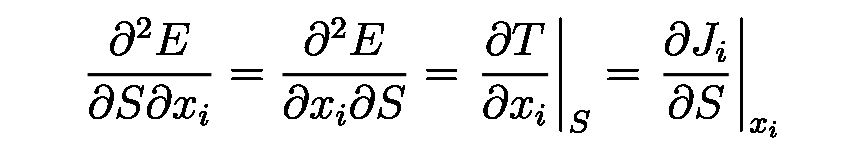

```mathematica
MaTeX["\\frac{\\partial^{2} E}{\\partial S \\partial x_{i}}=\\frac{\\partial^{2} E}{\\partial x_{i} \\partial S}=\\left.\\frac{\\partial T}{\\partial x_{i}}\\right|_{S}=\\left.\\frac{\\partial J_{i}}{\\partial S}\\right|_{x_{i}}", Magnification -> 4]
```

(58) -- Since $(\partial y / \partial x)=(\partial x / \partial y)^{-1}$, the above equation can be inverted to give

Statistical Mechanics
Ramirez (59)

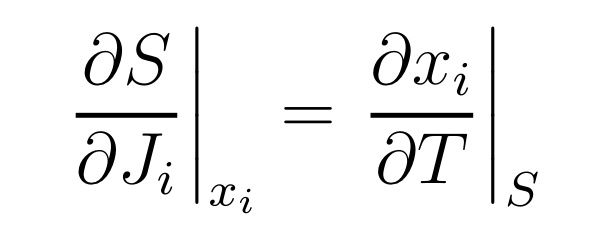

```mathematica
MaTeX["\\left.\\frac{\\partial S}{\\partial J_{i}}\\right|_{x_{i}}=\\left.\\frac{\\partial x_{i}}{\\partial T}\\right|_{S}", Magnification -> 4]
```

```mathematica
(60) -- Similar identities can be obtained from the variations of other state functions. Supposing that we are interested in finding an identity involving $\partial S /\left.\partial x\right|_{T}$. We would like to find a state function whose variations include $S d T$ and $J d x$. The correct choice is $d F=d(E-T S)=-S d T+J d x$. Looking at the second derivative of $F$ yields the Maxwell relation
```

Statistical Mechanics
Ramirez (61)

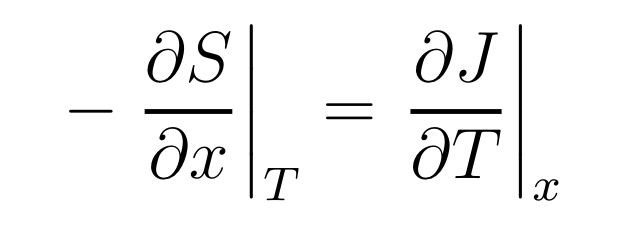

```mathematica
MaTeX["-\\left.\\frac{\\partial S}{\\partial x}\\right|_{T}=\\left.\\frac{\\partial J}{\\partial T}\\right|_{x}", Magnification -> 4]
```

(62) -- The entropy S of a system subjected to an external force J, represented by the generalized coordinate x, can be obtained by considering the differential expression d(E - TS - Jx) = -SdT - xdJ. This identity relates the changes in the system's energy E, temperature T, entropy S, and the generalized force J acting on the coordinate x. By taking the partial derivative of this expression with respect to J at constant temperature T, we can derive the expression for ∂S/∂J|T, which quantifies the influence of the external force on the system's entropy.

Statistical Mechanics
Ramirez (63)

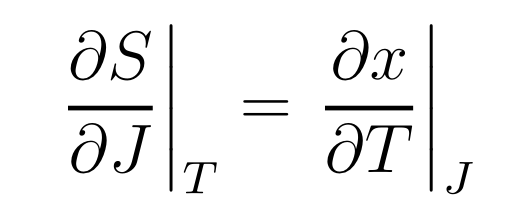

```mathematica
MaTeX["\\left.\\frac{\\partial S}{\\partial J}\\right|_{T}=\\left.\\frac{\\partial x}{\\partial T}\\right|_{J}", Magnification -> 4]
```

```mathematica
(64) -- There are a variety of mnemonics which are supposed to help you remember and construct Maxwell's equations, such as Magic Squares, Jacobians, etc. I personally don't find any of these methods worth learning. The most logical approach is to remember the laws of thermodynamics and hence eq.(I.28), and to then manipulate it so as to find the appropriate derivative using the rules of differentiation.
```

(65) -- To derive the expression for the partial derivative of chemical potential with respect to pressure at constant temperature and number of particles for an ideal gas, we begin with the fundamental thermodynamic relation:

d(E - TS + PV) = -SdT + VdP + μdN

Treating N, T as independent variables, we have:

(∂μ/∂P)_{N,T} = (∂(E - TS + PV)/∂P)_{N,T} = V

Thus, for an ideal gas, the partial derivative of chemical potential with respect to pressure at constant temperature and number of particles is simply the molar volume, V.

Statistical Mechanics
Ramirez (66)

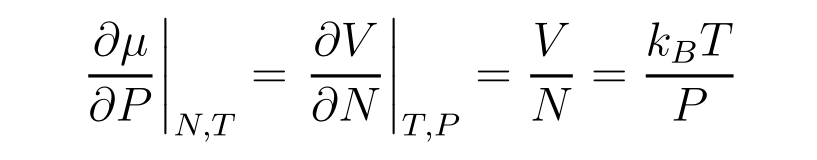

```mathematica
MaTeX["\\left.\\frac{\\partial \\mu}{\\partial P}\\right|_{N, T}=\\left.\\frac{\\partial V}{\\partial N}\\right|_{T, P}=\\frac{V}{N}=\\frac{k_{B} T}{P}", Magnification -> 4]
```

```mathematica
(67) -- as in eq.(I.50). From eq.(I.28) it also follows that
```

Statistical Mechanics
Ramirez (68)

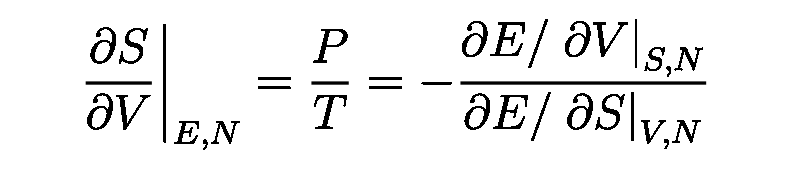

```mathematica
MaTeX["\\left.\\frac{\\partial S}{\\partial V}\\right|_{E, N}=\\frac{P}{T}=-\\frac{\\partial E /\\left.\\partial V\\right|_{S, N}}{\\partial E /\\left.\\partial S\\right|_{V, N}}", Magnification -> 4]
```

(69) -- where we have used eq.(I.45) for the final identity. The above equation can be rearranged into

Statistical Mechanics
Ramirez (70)

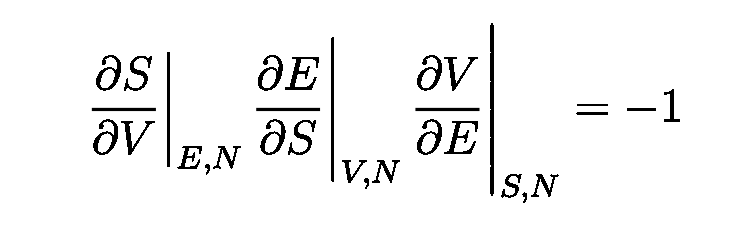

```mathematica
MaTeX["\\left.\\left.\\left.\\frac{\\partial S}{\\partial V}\\right|_{E, N} \\frac{\\partial E}{\\partial S}\\right|_{V, N} \\frac{\\partial V}{\\partial E}\\right|_{S, N}=-1", Magnification -> 4]
```

(71) -- The chain rule of differentiation is a fundamental concept in calculus that allows us to differentiate composite functions. It states that for a composite function f(g(x)), the derivative is given by:

(df/dx) = (df/dg) × (dg/dx)

This rule is essential in thermodynamics and statistical mechanics, where we often encounter complex functions involving multiple variables. For instance, when dealing with the entropy S as a function of energy E and volume V, we can apply the chain rule to find the differential relation:

dS = (∂S/∂E)_V dE + (∂S/∂V)_E dV

This expression reflects the fact that entropy changes can arise from variations in both energy and volume, and the partial derivatives capture the respective contributions. The chain rule is a powerful tool for analyzing such intricate relationships between thermodynamic quantities.

## Reference

https://assets.cambridge.org/97805218/73420/frontmatter/9780521873420_frontmatter.pdf

### All old notes:

https://drive.google.com/drive/u/0/folders/1pmmshVrJGU_j6wwc6zTNCo_CQAz9SJmD

```mathematica
mathPiXDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mathPiXDB/"<>mathPiXDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear